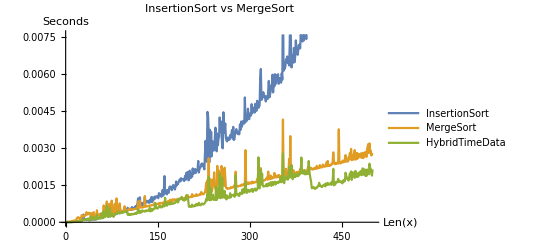

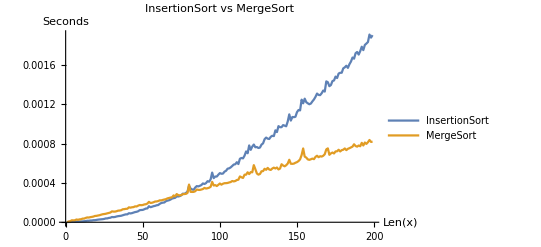

```mathematica
MergesortTimeData= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/mergeData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
InsertionTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/insertData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
HybridTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/hybridData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
ListLinePlot[{InsertionTimeData,MergesortTimeData,HybridTimeData}, PlotLegends->{"InsertionSort","MergeSort","HybridTimeData"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["InsertionSort vs MergeSort"],LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
data=Table[{i,ScientificForm@InsertionTimeData[[i]],ScientificForm@MergesortTimeData[[i]]}, {i,90,110}];
data2=Prepend[data,{"n","InsertionSort","Mergesort"}]
```

{{n,InsertionSort,Mergesort},{90,4.18837×10^-4,4.66314×10^-4},{91,4.20216×10^-4,4.76898×10^-4},{92,4.0984×10^-4,4.43814×10^-4},{93,4.14039×10^-4,4.48785×10^-4},{94,4.23485×10^-4,4.65383×10^-4},{95,4.34085×10^-4,4.53695×10^-4},{96,4.87659×10^-4,5.06538×10^-4},{97,4.51336×10^-4,4.71357×10^-4},{98,4.59073×10^-4,4.69494×10^-4},{99,4.72991×10^-4,4.95376×10^-4},{100,4.92354×10^-4,4.84251×10^-4},{101,4.96398×10^-4,5.22952×10^-4},{102,5.25212×10^-4,5.28316×10^-4},{103,5.05212×10^-4,5.0213×10^-4},{104,5.13915×10^-4,5.06119×10^-4},{105,5.24486×10^-4,5.30281×10^-4},{106,5.35288×10^-4,5.21656×10^-4},{107,5.34988×10^-4,5.19788×10^-4},{108,5.52923×10^-4,5.30629×10^-4},{109,5.69821×10^-4,5.37503×10^-4},{110,6.13861×10^-4,5.82557×10^-4}}

```mathematica
griddata=Grid[data2,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

n | BST | Hash Table
1 | 1.2412×10^4 | 1.8934×10^4
2 | 5.7676×10^4 | 1.0012×10^4
3 | 5.728×10^3 | 7.138×10^3
4 | 1.1188×10^4 | 1.2892×10^4
5 | 2.7252×10^4 | 3.9026×10^4
6 | 4.265×10^4 | 3.9168×10^4
7 | 8.9084×10^4 | 7.8034×10^4
8 | 1.37448×10^5 | 1.31526×10^5
9 | 2.75757×10^5 | 2.44719×10^5
10 | 5.71288×10^5 | 4.92816×10^5
11 | 1.25169×10^6 | 1.01215×10^6
12 | 1.85738×10^6 | 1.30203×10^6
13 | 4.64203×10^6 | 3.15917×10^6
14 | 9.75582×10^6 | 6.29125×10^6
15 | 1.79836×10^7 | 1.19833×10^7
16 | 4.70545×10^7 | 2.99676×10^7
17 | 9.54767×10^7 | 6.17532×10^7
18 | 2.43529×10^8 | 1.43255×10^8
19 | 5.74542×10^8 | 3.0654×10^8
20 | 1.3443806860000000×10^9 | 6.57059×10^8
21 | 3.0514876590000000×10^9 | 1.3660087510000000×10^9
22 | 6.6160220150000000×10^9 | 2.7909349340000000×10^9
23 | 1.50265328690000000×10^10 | 6.0042416900000000×10^9

```mathematica
Insert[griddata,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

n | BST | Hash Table
1 | 1.2412×10^4 | 1.8934×10^4
2 | 5.7676×10^4 | 1.0012×10^4
3 | 5.728×10^3 | 7.138×10^3
4 | 1.1188×10^4 | 1.2892×10^4
5 | 2.7252×10^4 | 3.9026×10^4
6 | 4.265×10^4 | 3.9168×10^4
7 | 8.9084×10^4 | 7.8034×10^4
8 | 1.37448×10^5 | 1.31526×10^5
9 | 2.75757×10^5 | 2.44719×10^5
10 | 5.71288×10^5 | 4.92816×10^5
11 | 1.25169×10^6 | 1.01215×10^6
12 | 1.85738×10^6 | 1.30203×10^6
13 | 4.64203×10^6 | 3.15917×10^6
14 | 9.75582×10^6 | 6.29125×10^6
15 | 1.79836×10^7 | 1.19833×10^7
16 | 4.70545×10^7 | 2.99676×10^7
17 | 9.54767×10^7 | 6.17532×10^7
18 | 2.43529×10^8 | 1.43255×10^8
19 | 5.74542×10^8 | 3.0654×10^8
20 | 1.3443806860000000×10^9 | 6.57059×10^8
21 | 3.0514876590000000×10^9 | 1.3660087510000000×10^9
22 | 6.6160220150000000×10^9 | 2.7909349340000000×10^9
23 | 1.50265328690000000×10^10 | 6.0042416900000000×10^9

```mathematica
TableForm[%58]
```

90 | 4.18837×10^-4 | 4.66314×10^-4
91 | 4.20216×10^-4 | 4.76898×10^-4
92 | 4.0984×10^-4 | 4.43814×10^-4
93 | 4.14039×10^-4 | 4.48785×10^-4
94 | 4.23485×10^-4 | 4.65383×10^-4
95 | 4.34085×10^-4 | 4.53695×10^-4
96 | 4.87659×10^-4 | 5.06538×10^-4
97 | 4.51336×10^-4 | 4.71357×10^-4
98 | 4.59073×10^-4 | 4.69494×10^-4
99 | 4.72991×10^-4 | 4.95376×10^-4
100 | 4.92354×10^-4 | 4.84251×10^-4
101 | 4.96398×10^-4 | 5.22952×10^-4
102 | 5.25212×10^-4 | 5.28316×10^-4
103 | 5.05212×10^-4 | 5.0213×10^-4
104 | 5.13915×10^-4 | 5.06119×10^-4
105 | 5.24486×10^-4 | 5.30281×10^-4
106 | 5.35288×10^-4 | 5.21656×10^-4
107 | 5.34988×10^-4 | 5.19788×10^-4
108 | 5.52923×10^-4 | 5.30629×10^-4
109 | 5.69821×10^-4 | 5.37503×10^-4
110 | 6.13861×10^-4 | 5.82557×10^-4

```mathematica
TableForm[%56]
```

90 | 0.000418837 | 0.000466314
91 | 0.000420216 | 0.000476898
92 | 0.00040984 | 0.000443814
93 | 0.000414039 | 0.000448785
94 | 0.000423485 | 0.000465383
95 | 0.000434085 | 0.000453695
96 | 0.000487659 | 0.000506538
97 | 0.000451336 | 0.000471357
98 | 0.000459073 | 0.000469494
99 | 0.000472991 | 0.000495376
100 | 0.000492354 | 0.000484251
101 | 0.000496398 | 0.000522952
102 | 0.000525212 | 0.000528316
103 | 0.000505212 | 0.00050213
104 | 0.000513915 | 0.000506119
105 | 0.000524486 | 0.000530281
106 | 0.000535288 | 0.000521656
107 | 0.000534988 | 0.000519788
108 | 0.000552923 | 0.000530629
109 | 0.000569821 | 0.000537503
110 | 0.000613861 | 0.000582557

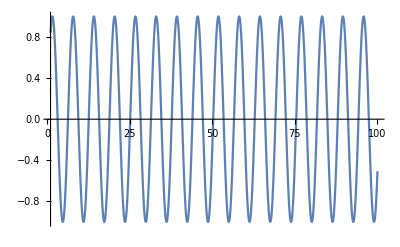

```mathematica
Plot[Sin[x],{x,1,100}]
```

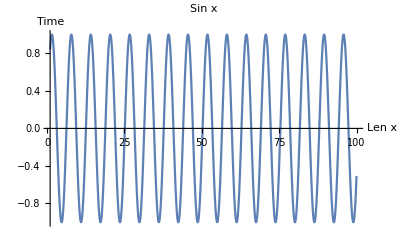

```mathematica
Show[%29,AxesLabel->{HoldForm[Len x],HoldForm[Time]},PlotLabel->HoldForm[Sin x],LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
ListPlot[{Labeled[Sqrt[Range[40]],"sqrt"],Labeled[Log[Range[40,80]],"log"]}]
```

```mathematica
List
```

```mathematica
5e-4
```

-4+5 e

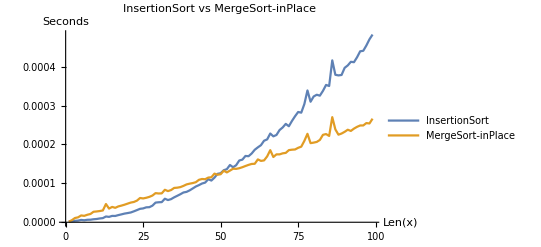

```mathematica
MergesortTimeData= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/mergeData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
InsertionTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/insertData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
ListLinePlot[{InsertionTimeData,MergesortTimeData}, PlotLegends->{"InsertionSort","MergeSort-inPlace"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["InsertionSort vs MergeSort-inPlace"],LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
MergesortTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/mergeData.txt"],{"e" "*^","["->"{","]"->"}"}];
InsertionTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/insertData.txt"],{"e" \"*^", "[" -> "{", "]" -> "}"}];
ListLinePlot[{InsertionTimeData, MergesortTimeData}, 
 PlotLegends -> {"InsertionSort", "MergeSort"}, 
 AxesLabel -> {HoldForm["Len(x)"], HoldForm["Seconds"]}, 
 PlotLabel -> HoldForm["InsertionSort vs MergeSort"], 
 LabelStyle -> {14, GrayLevel[0]}]
```

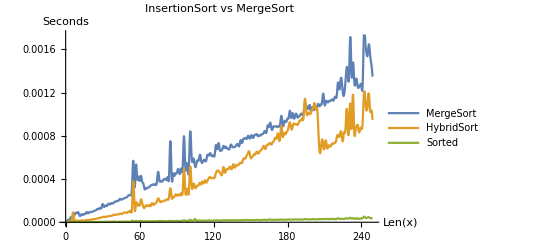

```mathematica
MergesortTimeData= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/mergeData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
InsertionTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/insertData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
HybridTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/hybridData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
SortedTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/sortedData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
ListLinePlot[{MergesortTimeData,HybridTimeData,SortedTimeData},InterpolationOrder->5,Joined->True,PlotRange->All, PlotLegends->{"MergeSort","HybridSort","Sorted"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["InsertionSort vs MergeSort"],LabelStyle->{14,GrayLevel[0]}]
```

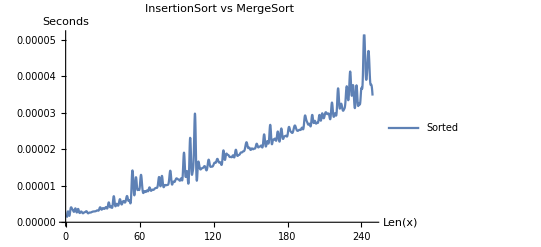

```mathematica
ListLinePlot[{SortedTimeData},InterpolationOrder->5,Joined->True,PlotRange->All, PlotLegends->{"Sorted"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["InsertionSort vs MergeSort"],LabelStyle->{14,GrayLevel[0]}]
```

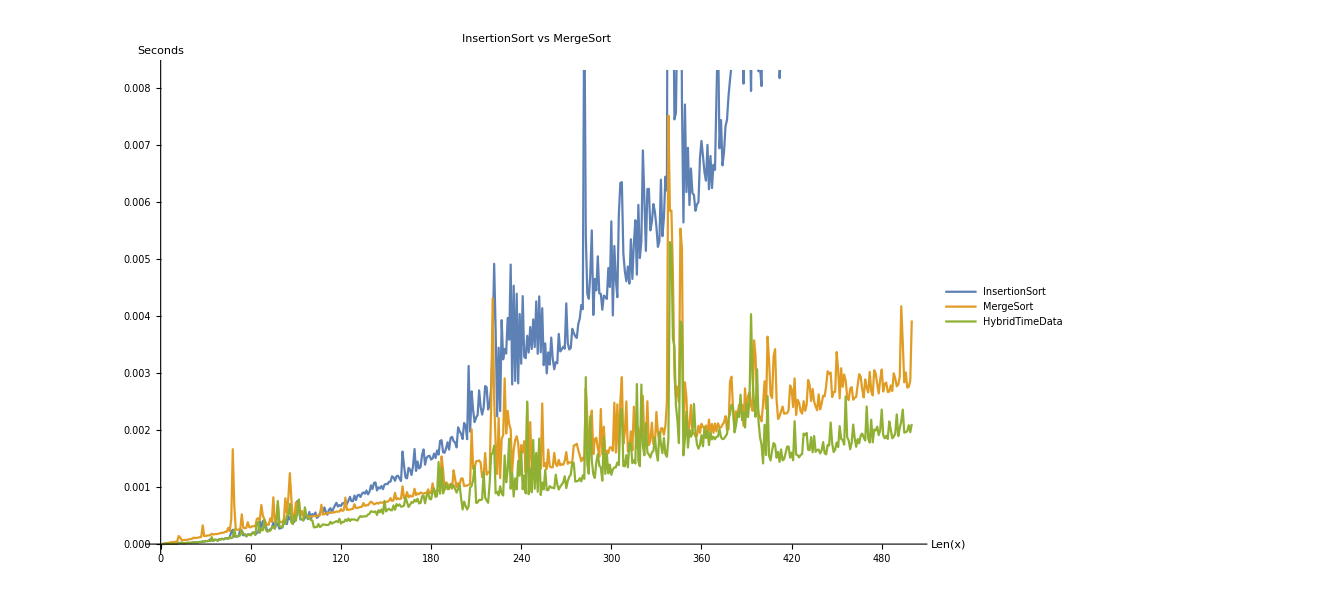

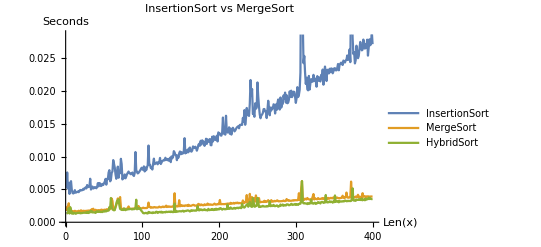

```mathematica
MergesortTimeData= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/mergeData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
InsertionTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/insertData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
HybridTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/hybridData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
ListLinePlot[{InsertionTimeData,MergesortTimeData,HybridTimeData}, PlotLegends->{"InsertionSort","MergeSort","HybridSort"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["InsertionSort vs MergeSort"],LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
ListCurvePathPlot[
```

```mathematica
MergesortTimeData= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/mergeData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
InsertionTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/insertData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
HybridTimeData=ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/hybridData.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
ListCurvePathPlot[{InsertionTimeData,MergesortTimeData,HybridTimeData}, PlotLegends->{"InsertionSort","MergeSort","HybridSort"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["InsertionSort vs MergeSort"],LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
data=Table[{i,MergesortTimeData[[i]]},{i,1,200}]
```

{{1,1.35903×10^-6},{2,9.88017×10^-7},{3,0.000016416},{4,0.000017172},{5,0.000029562},{6,0.000026442},{7,0.000028805},{8,0.0000373869},{9,0.000038163},{10,0.0000432549},{11,0.000046064},{12,0.0000494811},{13,0.000054664},{14,0.000060773},{15,0.0000649},{16,0.0000707919},{17,0.000074378},{18,0.0000809539},{19,0.0000845849},{20,0.000091124},{21,0.00009488},{22,0.000205528},{23,0.000109943},{24,0.000110777},{25,0.000114565},{26,0.000209802},{27,0.000125832},{28,0.000130745},{29,0.000132236},{30,0.000140107},{31,0.000144864},{32,0.000161967},{33,0.000160684},{34,0.000162013},{35,0.000167939},{36,0.000176599},{37,0.000176615},{38,0.00018383},{39,0.000199199},{40,0.000193791},{41,0.000392078},{42,0.000358085},{43,0.000221942},{44,0.000214287},{45,0.000230524},{46,0.000524919},{47,0.000238715},{48,0.000232879},{49,0.000242168},{50,0.000437847},{51,0.000337791},{52,0.000259722},{53,0.000260409},{54,0.000271011},{55,0.000568436},{56,0.000285561},{57,0.000284594},{58,0.000310234},{59,0.000625451},{60,0.000451451},{61,0.000318014},{62,0.000387206},{63,0.000322776},{64,0.000437561},{65,0.000476631},{66,0.000662846},{67,0.000355207},{68,0.000351699},{69,0.000346614},{70,0.000445154},{71,0.00106607},{72,0.000363817},{73,0.000345405},{74,0.000346196},{75,0.00034731},{76,0.000467994},{77,0.000754617},{78,0.00080008},{79,0.000647162},{80,0.000583134},{81,0.000893498},{82,0.000471321},{83,0.000401301},{84,0.000650632},{85,0.000409273},{86,0.000406844},{87,0.00041071},{88,0.000414951},{89,0.000442677},{90,0.00044694},{91,0.000431075},{92,0.00058125},{93,0.000472462},{94,0.000464805},{95,0.000450075},{96,0.000457451},{97,0.000552099},{98,0.000466348},{99,0.000483657},{100,0.0004729},{101,0.000591054},{102,0.000487319},{103,0.00049131},{104,0.000496023},{105,0.000498877},{106,0.000596999},{107,0.000516673},{108,0.000520884},{109,0.000530777},{110,0.000534947},{111,0.000545939},{112,0.000616027},{113,0.000539224},{114,0.000586716},{115,0.000559931},{116,0.000554227},{117,0.000725308},{118,0.000566389},{119,0.000578938},{120,0.000586477},{121,0.000576285},{122,0.000589169},{123,0.000599377},{124,0.000614889},{125,0.000601852},{126,0.000602596},{127,0.000761155},{128,0.000618058},{129,0.000804964},{130,0.000707448},{131,0.000632015},{132,0.000642964},{133,0.00064612},{134,0.000702171},{135,0.000659897},{136,0.000672243},{137,0.000739879},{138,0.000676132},{139,0.000769816},{140,0.000697425},{141,0.00068362},{142,0.000688663},{143,0.000697014},{144,0.000783439},{145,0.000710133},{146,0.000761484},{147,0.000727489},{148,0.00072362},{149,0.000728282},{150,0.000904397},{151,0.000760283},{152,0.000761661},{153,0.000755558},{154,0.000760239},{155,0.000776992},{156,0.00103623},{157,0.000777639},{158,0.000788538},{159,0.000840076},{160,0.00110189},{161,0.00085254},{162,0.000802022},{163,0.000813198},{164,0.000873218},{165,0.000819929},{166,0.000824622},{167,0.000919322},{168,0.000835104},{169,0.00090734},{170,0.00086802},{171,0.00087809},{172,0.000857211},{173,0.000911463},{174,0.00092706},{175,0.000884242},{176,0.000966774},{177,0.000971383},{178,0.000891365},{179,0.000900025},{180,0.000899736},{181,0.000909281},{182,0.000945001},{183,0.000918434},{184,0.00115543},{185,0.00104101},{186,0.000929494},{187,0.000945528},{188,0.00110028},{189,0.00103744},{190,0.000953042},{191,0.000955344},{192,0.000967298},{193,0.000966047},{194,0.00120704},{195,0.000986327},{196,0.00104717},{197,0.00110438},{198,0.00100026},{199,0.00100686},{200,0.00100997}}

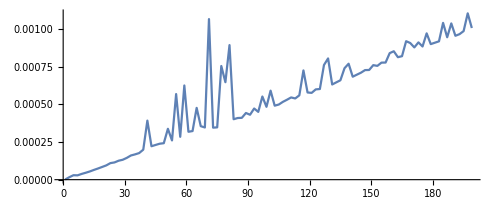

```mathematica
ListCurvePathPlot[{data}]
```

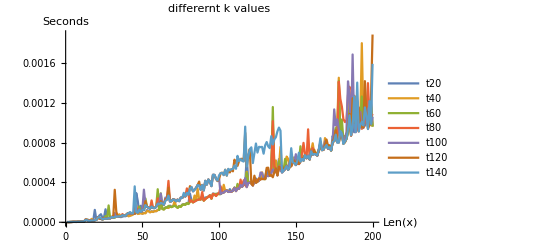

```mathematica
t20= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t20.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t40= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t40.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t60= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t60.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t80= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t80.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t100= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t100.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t120= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t120.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t140= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t140.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
ListLinePlot[{t20,t40,t60,t80,t100,t120,t140}, PlotLegends->{"t20","t40","t60","t80","t100","t120","t140"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["differernt k values"],LabelStyle->{14,GrayLevel[0]}]
```

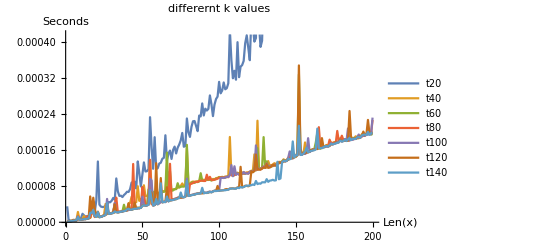

```mathematica
ListLinePlot[{t20,t40,t60,t80,t100,t120,t140}, PlotLegends->{"t20","t40","t60","t80","t100","t120","t140"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["differernt k values"],LabelStyle->{14,GrayLevel[0]}]
```

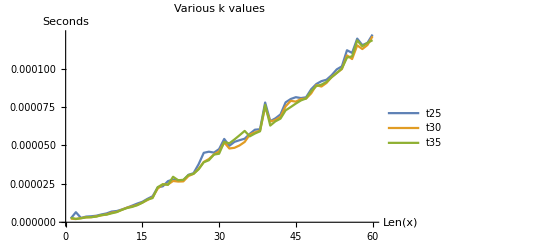

```mathematica
t20= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t20.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t40= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t40.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t60= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t60.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t80= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t80.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t100= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t100.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t120= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t120.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t140= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t140.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
ListLinePlot[{t100,t120,t140}, PlotLegends->{"t25","t30","t35"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["Various k values"],LabelStyle->{14,GrayLevel[0]}]
```

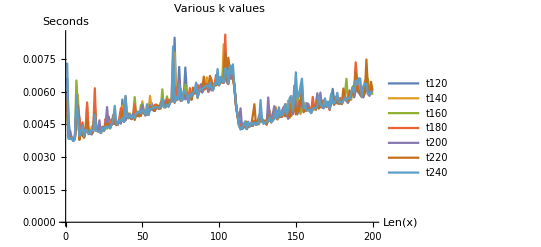

```mathematica
t20= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t20.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t40= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t40.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t60= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t60.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t80= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t80.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t100= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t100.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t120= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t120.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t140= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t140.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
ListLinePlot[{t20,t40,t60,t80,t100,t120,t140}, PlotLegends->{"t120","t140","t160","t180","t200","t220","t240"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["Various k values"],LabelStyle->{14,GrayLevel[0]}]
```

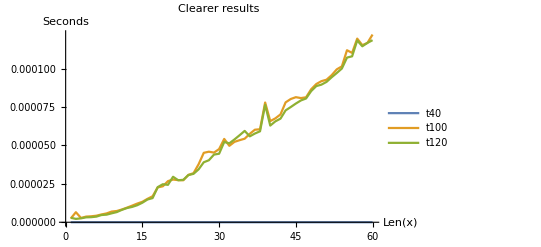

```mathematica
t20= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t20.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t40= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t40.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t60= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t60.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t80= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t80.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t100= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t100.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t120= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t120.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
t140= ToExpression@StringReplace[Import["/Users/andres/Desktop/EECS431/HW4/t140.txt"], {"e"-> "*^","["-> "{","]"-> "}"}];
ListLinePlot[{t40,t100,t140}, PlotLegends->{"t40","t100","t120"}, AxesLabel->{HoldForm["Len(x)"],HoldForm["Seconds"]},PlotLabel->HoldForm["Clearer results"],LabelStyle->{14,GrayLevel[0]}]
```

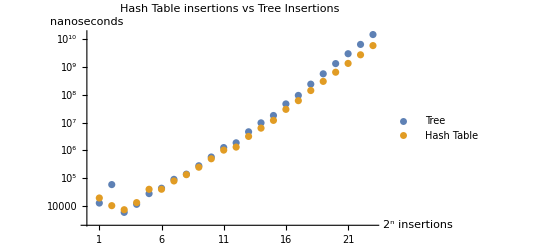

```mathematica
setData =ToExpression@StringSplit@Import["/Users/andres/Desktop/EECS431/set.txt"];
usetData =ToExpression@StringSplit@Import["/Users/andres/Desktop/EECS431/uset.txt"];
ListLogPlot[{setData, usetData},Ticks-> {Range[1,23],Automatic}, PlotLegends->{"Tree","Hash Table"}, AxesLabel->{HoldForm["2^n insertions"],HoldForm["nanoseconds"]},PlotLabel->HoldForm["Hash Table insertions vs Tree Insertions"],LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
data=Table[{i,ScientificForm@setData[[i]],ScientificForm@usetData[[i]]}, {i,1,Length[setData]}];
data2=Prepend[data,{"n","BST","Hash Table"}]
```

{{n,BST,Hash Table},{1,1.2412×10^4,1.8934×10^4},{2,5.7676×10^4,1.0012×10^4},{3,5.728×10^3,7.138×10^3},{4,1.1188×10^4,1.2892×10^4},{5,2.7252×10^4,3.9026×10^4},{6,4.265×10^4,3.9168×10^4},{7,8.9084×10^4,7.8034×10^4},{8,1.37448×10^5,1.31526×10^5},{9,2.75757×10^5,2.44719×10^5},{10,5.71288×10^5,4.92816×10^5},{11,1.25169×10^6,1.01215×10^6},{12,1.85738×10^6,1.30203×10^6},{13,4.64203×10^6,3.15917×10^6},{14,9.75582×10^6,6.29125×10^6},{15,1.79836×10^7,1.19833×10^7},{16,4.70545×10^7,2.99676×10^7},{17,9.54767×10^7,6.17532×10^7},{18,2.43529×10^8,1.43255×10^8},{19,5.74542×10^8,3.0654×10^8},{20,1.3443806860000000×10^9,6.57059×10^8},{21,3.0514876590000000×10^9,1.3660087510000000×10^9},{22,6.6160220150000000×10^9,2.7909349340000000×10^9},{23,1.50265328690000000×10^10,6.0042416900000000×10^9}}

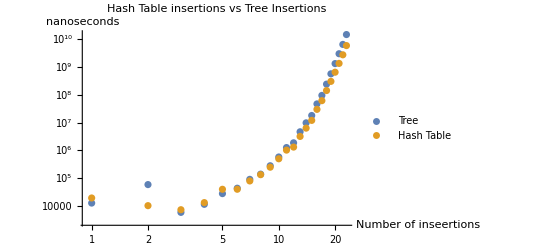

```mathematica
setData =ToExpression@StringSplit@Import["/Users/andres/Desktop/EECS431/set.txt"];
usetData =ToExpression@StringSplit@Import["/Users/andres/Desktop/EECS431/uset.txt"];
ListLogLogPlot[{setData, usetData}, PlotLegends->{"Tree","Hash Table"}, AxesLabel->{HoldForm["Number of inseertions"],HoldForm["nanoseconds"]},PlotLabel->HoldForm["Hash Table insertions vs Tree Insertions"],LabelStyle->{14,GrayLevel[0]}]
```

```mathematica
f[x_]:=
```

```mathematica
f[5]
```

2^x

```mathematica
data=Table[{Superscript[2,i],ScientificForm[setData[[i]],5],ScientificForm[usetData[[i]],5], NumberForm[#,2]&[setData[[i]]/usetData[[i]]]}, {i,1,Length[setData]}];
data2=Prepend[data,{"Insertions","BST","Hash Table","ratio bst to HT"}];
griddata=Grid[data2,Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

Insertions | BST | Hash Table | ratio bst to HT
2^1 | 1.2412×10^4 | 1.8934×10^4 | 0.66
2^2 | 5.7676×10^4 | 1.0012×10^4 | 5.8
2^3 | 5.728×10^3 | 7.138×10^3 | 0.8
2^4 | 1.1188×10^4 | 1.2892×10^4 | 0.87
2^5 | 2.7252×10^4 | 3.9026×10^4 | 0.7
2^6 | 4.265×10^4 | 3.9168×10^4 | 1.1
2^7 | 8.9084×10^4 | 7.8034×10^4 | 1.1
2^8 | 1.3745×10^5 | 1.3153×10^5 | 1.
2^9 | 2.7576×10^5 | 2.4472×10^5 | 1.1
2^10 | 5.7129×10^5 | 4.9282×10^5 | 1.2
2^11 | 1.2517×10^6 | 1.0122×10^6 | 1.2
2^12 | 1.8574×10^6 | 1.302×10^6 | 1.4
2^13 | 4.642×10^6 | 3.1592×10^6 | 1.5
2^14 | 9.7558×10^6 | 6.2912×10^6 | 1.6
2^15 | 1.7984×10^7 | 1.1983×10^7 | 1.5
2^16 | 4.7054×10^7 | 2.9968×10^7 | 1.6
2^17 | 9.5477×10^7 | 6.1753×10^7 | 1.5
2^18 | 2.4353×10^8 | 1.4325×10^8 | 1.7
2^19 | 5.7454×10^8 | 3.0654×10^8 | 1.9
2^20 | 1.3444×10^9 | 6.5706×10^8 | 2.
2^21 | 3.0515×10^9 | 1.3660×10^9 | 2.2
2^22 | 6.6160×10^9 | 2.7909×10^9 | 2.4
2^23 | 1.5027×10^10 | 6.0042×10^9 | 2.5

num of Insertions | BST | Hash Table
2^1 | 1.2412×10^4 | 1.8934×10^4
2^2 | 5.7676×10^4 | 1.0012×10^4
2^3 | 5.728×10^3 | 7.138×10^3
2^4 | 1.1188×10^4 | 1.2892×10^4
2^5 | 2.7252×10^4 | 3.9026×10^4
2^6 | 4.265×10^4 | 3.9168×10^4
2^7 | 8.9084×10^4 | 7.8034×10^4
2^8 | 1.37448×10^5 | 1.31526×10^5
2^9 | 2.75757×10^5 | 2.44719×10^5
2^10 | 5.71288×10^5 | 4.92816×10^5
2^11 | 1.25169×10^6 | 1.01215×10^6
2^12 | 1.85738×10^6 | 1.30203×10^6
2^13 | 4.64203×10^6 | 3.15917×10^6
2^14 | 9.75582×10^6 | 6.29125×10^6
2^15 | 1.79836×10^7 | 1.19833×10^7
2^16 | 4.70545×10^7 | 2.99676×10^7
2^17 | 9.54767×10^7 | 6.17532×10^7
2^18 | 2.43529×10^8 | 1.43255×10^8
2^19 | 5.74542×10^8 | 3.0654×10^8
2^20 | 1.3443806860000000×10^9 | 6.57059×10^8
2^21 | 3.0514876590000000×10^9 | 1.3660087510000000×10^9
2^22 | 6.6160220150000000×10^9 | 2.7909349340000000×10^9
2^23 | 1.50265328690000000×10^10 | 6.0042416900000000×10^9

```mathematica
Insert[griddata,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

Insertions | BST | Hash Table | ratio bst to HT
2^1 | 1.2412×10^4 | 1.8934×10^4 | 0.66
2^2 | 5.7676×10^4 | 1.0012×10^4 | 5.8
2^3 | 5.728×10^3 | 7.138×10^3 | 0.8
2^4 | 1.1188×10^4 | 1.2892×10^4 | 0.87
2^5 | 2.7252×10^4 | 3.9026×10^4 | 0.7
2^6 | 4.265×10^4 | 3.9168×10^4 | 1.1
2^7 | 8.9084×10^4 | 7.8034×10^4 | 1.1
2^8 | 1.3745×10^5 | 1.3153×10^5 | 1.
2^9 | 2.7576×10^5 | 2.4472×10^5 | 1.1
2^10 | 5.7129×10^5 | 4.9282×10^5 | 1.2
2^11 | 1.2517×10^6 | 1.0122×10^6 | 1.2
2^12 | 1.8574×10^6 | 1.302×10^6 | 1.4
2^13 | 4.642×10^6 | 3.1592×10^6 | 1.5
2^14 | 9.7558×10^6 | 6.2912×10^6 | 1.6
2^15 | 1.7984×10^7 | 1.1983×10^7 | 1.5
2^16 | 4.7054×10^7 | 2.9968×10^7 | 1.6
2^17 | 9.5477×10^7 | 6.1753×10^7 | 1.5
2^18 | 2.4353×10^8 | 1.4325×10^8 | 1.7
2^19 | 5.7454×10^8 | 3.0654×10^8 | 1.9
2^20 | 1.3444×10^9 | 6.5706×10^8 | 2.
2^21 | 3.0515×10^9 | 1.3660×10^9 | 2.2
2^22 | 6.6160×10^9 | 2.7909×10^9 | 2.4
2^23 | 1.5027×10^10 | 6.0042×10^9 | 2.5

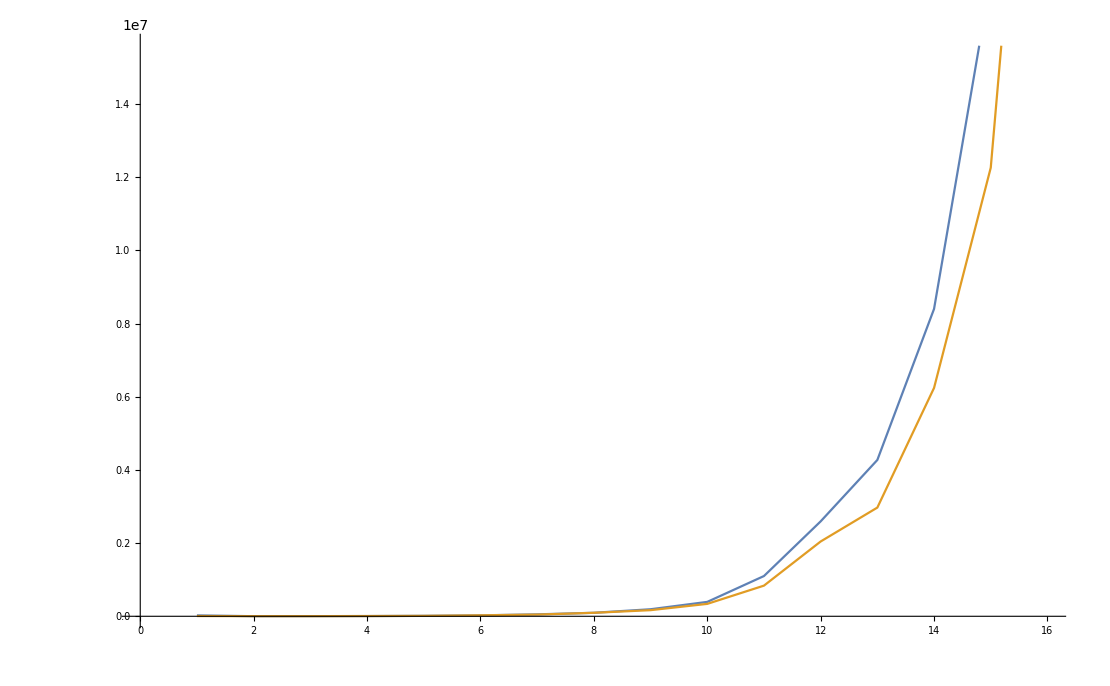

```mathematica
ListLinePlot[{setData, usetData}]
```